Input integration package and data for third surface - the face

```mathematica
SetDirectory[NotebookDirectory[]];
<<uniaxialintegratorV2`;
<<facedata`;
```

## Face: facedata.wl interpretation

Figure 3 includes a face like surface. 
The face is described by interpolating functions of its geometric properties as a function of the {x,y} Cartesian coordinates.
z coordinate: iz
Christoffel symbols: igammatry
Gaussian curvature: iK

These

```mathematica
faceplot=Plot3D[iz[x,y],{x,-16,16},{y,0,40},BoxRatios->Automatic,PlotStyle->Opacity[0.8]]
```

-Graphics3D-

Plot face’s gaussian curvature

```mathematica
Plot3D[iK[x,y],{x,-16,16},{y,0,40},PlotStyle->Opacity[0.8],PlotRange->All]
```

-Graphics3D-

## 4 surfaces with a face, numerical solution

## Inverse problem set up

Give material and surface properties

Designable features:

```mathematica
ϵ={ϵ1,ϵ2};
```

Deformation magnitude along and across the director:

```mathematica
λ1[epsilon_,lambda_]:=Exp[lambda[[1]] epsilon[[1]]];
λ2[epsilon_,lambda_]:=Exp[lambda[[2]] epsilon[[2]]];
```

Actuation values of the stimuli:

```mathematica
Λ={{0,0},{1/2,0},{2,0},{0,2}};
```

Target geometries:

```mathematica
g1=DiagonalMatrix[{1,1}]&;
g2=10^2{{1,0},{0,Sin[#[[1]]]^2}}&;
g3=ig@@#&;
g4=embeddingToMetric[{x,y, Sin[ x]Sin[ y/4]},{x,y}]@@#&
gList={g1,g2,g3,g4};
```

embeddingToMetric[{x,y,Sin[x] Sin[y/4]},{x,y}]@@#1&

Here we are integrating numerically specified surface geometries, and so we also supply the interpolated Gaussian curvatures and Christoffel symbols.

```mathematica
R1=exprToFunction[1/2 R[g1[{x,y}],{x,y}],{x,y}];
R2=exprToFunction[1/2 R[g2[{x,y}],{x,y}],{x,y}];
R3=iK;
R4=exprToFunction[1/2 R[g4[{x,y}],{x,y}],{x,y}];
Rlist={R1@@#&,R2@@#&,R3@@#&,R4@@#&};

Γlist=Table[If[surface==3,igammatry[[i,j,k]],exprToFunction[Γ[gList[[surface]]@{x,y},{x,y},i,j,k],{x,y}]],{surface,4},{i,2},{j,2},{k,2}];
```

We then verify that the problem is hyperbolic, and can be substantially solved from initial data:

```mathematica
CheckSolverValidity[λ1,λ2,ϵ,Λ]
```

Go ahead

ϵ1 and q1 initial conditions along u

ϵ2 and p2initial conditions along v

Finally, we derive the propagation equations for the inverse design of the sheet:

```mathematica
propagation=propagationInverseEqnsGivenGeometry[gList,Rlist,Γlist,λ1,λ2,ϵ,Λ];//AbsoluteTiming
```

{37.2514,Null}

and calculate where to assign the initial data for ϵ, along the initial u-curve or v-curve:

```mathematica
i12assignment=i12assign[λ1,λ2,ϵ,Λ]
```

{1,2}

## Give initial conditions

Initial u and v curves, specified parametrically on the initial surface:

```mathematica
ucurve[t_]=t{1,0};
vcurve[t_]=t{0,1};
```

Initial positions and directors on the target surfaces:

```mathematica
initialpositions={ucurve[0],{Pi/2,0},{0,18},{1,1}};
initialdirectors=MapThread[normalizevec[#1,#2[#3]]&,{{D[ucurve[t],t]/.t->0,{0,1},{0,1},{0,1}},{g1,g2,g3,g4},initialpositions}]
```

{{1,0},{0,1/10},{0.,0.995681},{0,1/(√(1+1/16 Cos[1/4]^2 Sin[1]^2))}}

Initial values of the designable features ϵ, and their derivatives p and q, given as parametric functions:

```mathematica
epsinitial[t_]={1/2,1/2};
pqinitial[t_]={0,0};
```

which are now collected

```mathematica
initialconditions={initialpositions,initialdirectors,epsinitial[t],pqinitial[t],ucurve[t],vcurve[t],gList[[1]],i12assignment};
```

We then test the initial conditions to verify that they are well posed at the origin:

```mathematica
testInitialData[propagation,initialconditions]
```

Propagation Equations and data at the origin are numeric

True

## Diagonal integrate

The inverse design problem is then integrated to obtain the fabrication data.
The data structure = Table[ {uv, r, n, α, β, ϵ, b, s, p, q},  {u,umax[[v]]}, {v,vmax}, {quad,4}]
Where quad - stands for the Cartesian quadrant in the (u,v) plane.
u, and v  enumerate u and v curves.
uv={u-value,v-value};
r={{x1,y1},{x2,y2},...,{xm,ym}} = A list of 2d coordinates on the initial and target surfaces.
n={{n1x,n1y},{n2x,n2y},...,{nmx,nmy}} = A list of images of the director on the initial and target surfaces.
α = arclength along u on the initial sheet.
β = arclength along v on the initial sheet.
ϵ= {ϵ1,ϵ2,...,ϵ_(m-1)} = list of designable features 
b= bend of director field
s= splay of director field
p={p1,p2,...,p_(m-1)} = list of variations of ϵ along u.
q={q1,q2,...,q_(m-1)} = list of variations of ϵ along v.

We now integrate the inverse problem with the following mesh setup:
maxdiag = maximal number of integration steps along each direction.
du  = step size along u,
dv =stepsize  along v, 
signu (signv)  = increase or decrease u (v);

```mathematica
intDiag[maxdiag_,signu_,signv_,du_,dv_]:=diagonalintegration[ucurve[t],vcurve[t],initialpositions,initialdirectors,epsinitial[t],pqinitial[t],λ1,λ2,Λ,gList,propagation,i12assignment,maxdiag,du,signu,dv,signv];
```

Build dataset:

```mathematica
ClearAll@@Table["data"<>ToString[i],{i,4}];
ClearAll[result]
ClearAll@@Table["vmax"<>ToString[i],{i,4}];
ClearAll@@Table["umaxtab"<>ToString[i],{i,4}];
datas=stringlist["data",4];
umaxtabs=stringlist["umaxtab",4];
vmaxs=stringlist["vmax",4];
quads={{1,1},{-1,1},{-1,-1},{1,-1}};
```

Integrate (this step is rather lengthy, with the current settings and a Mathematica 12.0 operating with a 2.6 GHz i7 core it takes a couple of hours):

```mathematica
maxdiag=100;
du=1/10;
dv=1/10;
(result=ParallelTable[intDiag[maxdiag,q[[1]],q[[2]],du,dv],{q,quads}];)//AbsoluteTiming
MapThread[Set[{#1,#2,#3},result[[#4]]]&,{umaxtabs,vmaxs,datas,Range[4]}];
```

ustop at {5, 44}

ustop at {5, 44}

vstop at {1, 74}

vstop at {1, 74}

{11665.5,Null}

## Plot Integrated Designable Elastic Features:

The director pattern to be fabricated is then:

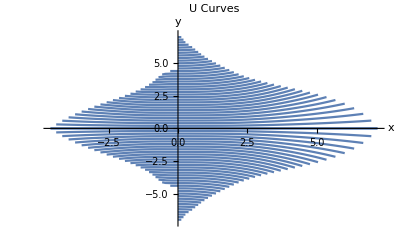

```mathematica
Show[Table[Table[ListLinePlot[datas[[quad,;;umaxtabs[[quad,vv]],vv,2,1]]],{vv,1,vmaxs[[quad,1]],2}],{quad,4}],PlotRange->All,PlotLabel->"U Curves",AxesLabel->{"x","y"}]
```

The designable features ϵ_1 and ϵ_2 to be fabricated are:

```mathematica
ListPointPlot3D[Join[#1,{#2}]&@@@Flatten[Table[Table[{#[[1,1]],#[[2,1]]}&/@datas[[quad,;;umaxtabs[[quad,vv]],vv,{2,6}]],{vv,vmaxs[[quad,1]]}],{quad,4}],2],PlotRange->All,PlotLabel->"Designable feature ϵ_1",AxesLabel->{"x","y","ϵ_1"}]
ListPointPlot3D[Join[#1,{#2}]&@@@Flatten[Table[Table[{#[[1,1]],#[[2,2]]}&/@datas[[quad,;;umaxtabs[[quad,vv]],vv,{2,6}]],{vv,vmaxs[[quad,1]]}],{quad,4}],2],PlotRange->All,PlotLabel->"Designable feature ϵ_2",AxesLabel->{"x","y","ϵ_2"}]
```

-Graphics3D-

-Graphics3D-

## Resulting 3D surfaces

The actuated surfaces then take the shapes:

```mathematica
fig3p1=Show[tubeEmbedColor[datas[[#]],umaxtabs[[#]],vmaxs[[#,1]],1,1,1,1,{x,y,0},{x,y}]&/@Range[4]]
fig3p2=Show[tubeEmbedColor[datas[[#]],umaxtabs[[#]],vmaxs[[#,1]],1,1,1,2,10RotationMatrix[-Pi/2,{0,1,0}].{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]},{θ,ϕ}]&/@Range[4]]
fig3p3=Show[tubeEmbedColor[datas[[#]],umaxtabs[[#]],vmaxs[[#,1]],1,1,1,3,{x,y,iz[x,y]},{x,y}]&/@Range[4]]
fig3p4=Show[tubeEmbedColor[datas[[#]],umaxtabs[[#]],vmaxs[[#,1]],1,1,1,4,{x,y, Sin[ x]Sin[ y/4]},{x,y}]&/@Range[4]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«1 more identical outputs»